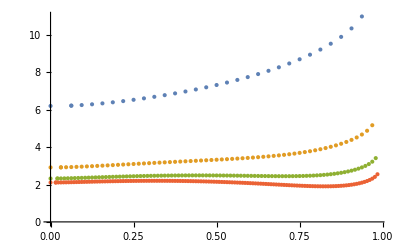

```mathematica
a2={{0,6.200516},{0.062500,6.217142},{0.062500,6.217142},{0.093750,6.248318},{0.125000,6.289166},{0.156250,6.338720},{0.187500,6.395887},{0.218750,6.459933},{0.250000,6.530395},{0.281250,6.607010},{0.312500,6.689671},{0.343750,6.778398},{0.375000,6.873327},{0.406250,6.974695},{0.437500,7.082840},{0.468750,7.198195},{0.500000,7.321298},{0.531250,7.452792},{0.562500,7.593444},{0.593750,7.744161},{0.625000,7.906028},{0.656250,8.080359},{0.687500,8.268778},{0.718750,8.473358},{0.750000,8.696849},{0.781250,8.943083},{0.812500,9.217728},{0.843750,9.529845},{0.875000,9.895548},{0.906250,10.348672},{0.937500,10.987524}};
c2={{0,11.653110},{0.062500,11.668284},{0.062500,11.668284},{0.093750,11.696001},{0.125000,11.731223},{0.156250,11.772652},{0.187500,11.818851},{0.218750,11.868738},{0.250000,11.921479},{0.281250,11.976419},{0.312500,12.033026},{0.343750,12.090865},{0.375000,12.149575},{0.406250,12.208854},{0.437500,12.268449},{0.468750,12.328150},{0.500000,12.387782},{0.531250,12.447203},{0.562500,12.506302},{0.593750,12.564996},{0.625000,12.623226},{0.656250,12.680962},{0.687500,12.738196},{0.718750,12.794946},{0.750000,12.851256},{0.781250,12.907195},{0.812500,12.962859},{0.843750,13.018371},{0.875000,13.073883},{0.906250,13.129578},{0.937500,13.185670},{0.968750,13.242408},{1.000000,13.300075},{1.031250,13.358997},{1.062500,13.419536},{1.093750,13.482102},{1.125000,13.547149},{1.156250,13.615182},{1.187500,13.686762},{1.218750,13.762504},{1.250000,13.843086},{1.281250,13.929251},{1.312500,14.021815},{1.343750,14.121669},{1.375000,14.229785},{1.406250,14.347230},{1.437500,14.475170},{1.468750,14.614886},{1.500000,14.767793},{1.531250,14.935460},{1.562500,15.119653},{1.593750,15.322381},{1.625000,15.545973},{1.656250,15.793197},{1.687500,16.067439},{1.718750,16.372992},{1.750000,16.715534},{1.781250,17.102970},{1.812500,17.546986},{1.843750,18.066236},{1.875000,18.693776},{1.906250,19.498624},{1.937500,20.679515}};
b2=c2*Table[{0.5,0.25},{i,0,62}];
f2={{0,20.874233},{0.062500,20.889319},{0.062500,20.889319},{0.093750,20.916822},{0.125000,20.951694},{0.156250,20.992612},{0.187500,21.038119},{0.218750,21.087105},{0.250000,21.138711},{0.281250,21.192250},{0.312500,21.247159},{0.343750,21.302966},{0.375000,21.359272},{0.406250,21.415727},{0.437500,21.472031},{0.468750,21.527917},{0.500000,21.583148},{0.531250,21.637515},{0.562500,21.690828},{0.593750,21.742917},{0.625000,21.793631},{0.656250,21.842830},{0.687500,21.890390},{0.718750,21.936198},{0.750000,21.980151},{0.781250,22.022157},{0.812500,22.062133},{0.843750,22.100005},{0.875000,22.135704},{0.906250,22.169172},{0.937500,22.200356},{0.968750,22.229212},{1.000000,22.255699},{1.031250,22.279786},{1.062500,22.301446},{1.093750,22.320659},{1.125000,22.337413},{1.156250,22.351701},{1.187500,22.363521},{1.218750,22.372882},{1.250000,22.379796},{1.281250,22.384284},{1.312500,22.386377},{1.343750,22.386111},{1.375000,22.383533},{1.406250,22.378699},{1.437500,22.371675},{1.468750,22.362539},{1.500000,22.351381},{1.531250,22.338303},{1.562500,22.323423},{1.593750,22.306873},{1.625000,22.288803},{1.656250,22.269381},{1.687500,22.248796},{1.718750,22.227258},{1.750000,22.205002},{1.781250,22.182288},{1.812500,22.159406},{1.843750,22.136676},{1.875000,22.114455},{1.906250,22.093132},{1.937500,22.073140},{1.968750,22.054954},{2.000000,22.039096},{2.031250,22.026139},{2.062500,22.016713},{2.093750,22.011504},{2.125000,22.011264},{2.156250,22.016812},{2.187500,22.029043},{2.218750,22.048930},{2.250000,22.077531},{2.281250,22.115996},{2.312500,22.165574},{2.343750,22.227620},{2.375000,22.303608},{2.406250,22.395140},{2.437500,22.503964},{2.468750,22.631992},{2.500000,22.781331},{2.531250,22.954317},{2.562500,23.153575},{2.593750,23.382096},{2.625000,23.643355},{2.656250,23.941490},{2.687500,24.281581},{2.718750,24.670085},{2.750000,25.115575},{2.781250,25.630002},{2.812500,26.231059},{2.843750,26.946990},{2.875000,27.827800},{2.906250,28.977706},{2.937500,30.695868}};
e2=f2*Table[{1/3,1/9},{i,0,94}];
h2={{0,33.699830},{0.062500,33.714912},{0.062500,33.714912},{0.093750,33.742403},{0.125000,33.777257},{0.156250,33.818150},{0.187500,33.863621},{0.218750,33.912561},{0.250000,33.964109},{0.281250,34.017576},{0.312500,34.072398},{0.343750,34.128102},{0.375000,34.184283},{0.406250,34.240594},{0.437500,34.296729},{0.468750,34.352419},{0.500000,34.407424},{0.531250,34.461530},{0.562500,34.514545},{0.593750,34.566293},{0.625000,34.616618},{0.656250,34.665375},{0.687500,34.712434},{0.718750,34.757673},{0.750000,34.800982},{0.781250,34.842262},{0.812500,34.881417},{0.843750,34.918363},{0.875000,34.953019},{0.906250,34.985314},{0.937500,35.015178},{0.968750,35.042550},{1.000000,35.067372},{1.031250,35.089589},{1.062500,35.109152},{1.093750,35.126014},{1.125000,35.140134},{1.156250,35.151470},{1.187500,35.159987},{1.218750,35.165651},{1.250000,35.168429},{1.281250,35.168294},{1.312500,35.165218},{1.343750,35.159176},{1.375000,35.150147},{1.406250,35.138110},{1.437500,35.123046},{1.468750,35.104939},{1.500000,35.083774},{1.531250,35.059537},{1.562500,35.032218},{1.593750,35.001807},{1.625000,34.968296},{1.656250,34.931680},{1.687500,34.891954},{1.718750,34.849116},{1.750000,34.803166},{1.781250,34.754107},{1.812500,34.701942},{1.843750,34.646677},{1.875000,34.588323},{1.906250,34.526890},{1.937500,34.462393},{1.968750,34.394850},{2.000000,34.324282},{2.031250,34.250713},{2.062500,34.174172},{2.093750,34.094693},{2.125000,34.012313},{2.156250,33.927074},{2.187500,33.839027},{2.218750,33.748225},{2.250000,33.654732},{2.281250,33.558616},{2.312500,33.459957},{2.343750,33.358841},{2.375000,33.255366},{2.406250,33.149642},{2.437500,33.041788},{2.468750,32.931942},{2.500000,32.820251},{2.531250,32.706884},{2.562500,32.592025},{2.593750,32.475878},{2.625000,32.358670},{2.656250,32.240652},{2.687500,32.122102},{2.718750,32.003324},{2.750000,31.884657},{2.781250,31.766473},{2.812500,31.649183},{2.843750,31.533236},{2.875000,31.419130},{2.906250,31.307408},{2.937500,31.198668},{2.968750,31.093566},{3.000000,30.992817},{3.031250,30.897205},{3.062500,30.807587},{3.093750,30.724895},{3.125000,30.650147},{3.156250,30.584451},{3.187500,30.529008},{3.218750,30.485127},{3.250000,30.454224},{3.281250,30.437837},{3.312500,30.437632},{3.343750,30.455415},{3.375000,30.493144},{3.406250,30.552947},{3.437500,30.637143},{3.468750,30.748266},{3.500000,30.889108},{3.531250,31.062765},{3.562500,31.272717},{3.593750,31.522934},{3.625000,31.818034},{3.656250,32.163525},{3.687500,32.566181},{3.718750,33.034630},{3.750000,33.580337},{3.781250,34.219307},{3.812500,34.975245},{3.843750,35.885995},{3.875000,37.018518},{3.906250,38.512237},{3.937500,40.766752}};
g2=h2*Table[{0.25,1/16},{i,0,126}];
ListPlot[{a2,b2,e2,g2},PlotRange->All]
```

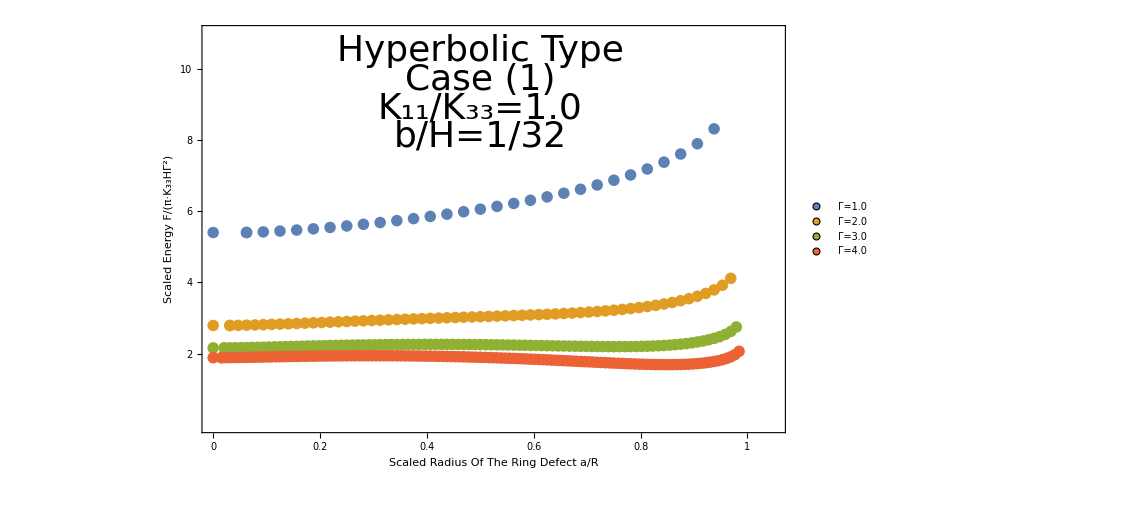

```mathematica
ListPlot[{a,b,e,g},PlotStyle->PointSize[0.01], Frame->{True, True, True, True}, FrameTicks->{{{2,4,6,8,10},None},{{0,0.2, 0.4, 0.6, 0.8,1},None}}, PlotRange->{{0,1.05},{0,11}},FrameLabel->{{"Scaled Energy F/(π·K_33HΓ^2)", None},{"Scaled Radius Of The Ring Defect a/R", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"Γ=1.0","Γ=2.0","Γ=3.0","Γ=4.0"},LegendMarkers->{{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12}}],{Left, Top}],Epilog->{Text[Style["Hyperbolic Type",Directive[Black,36]],{0.5,10.5}],Text[Style["Case (1)",Directive[Black,36]],{0.5,9.7}],Text[Style["K_11/K_33=1.0",Directive[Black,36]],{0.5,8.9}],Text[Style["b/H=1/32",Directive[Black,36]],{0.5,8.1}]}]
```